```mathematica
LagrangePoly[x0_,f0_]:=
Module[{xi=x0,fi=f0,n,m,ploy},n=Length[xi];
m=Length[fi];
If[n≠m,Print["List of points and function values are not of same size"];];
For[i=1,i≤n,i++,L[i,x_]=(Product[Divide[x-xi[[j]],xi[[i]]-xi[[j]]],{j,i-1}])*(Product[Divide[x-xi[[j]],xi[[i]]-xi[[j]]],{j,i+1,n}]);];
poly[x_]=Sum[L[k,x]*fi[[k]],{k,n}];
Return[poly[x]];]
Question 1
abscissas={0,1,3};
functionvalues={1,3,55};
LagrangePoly[x_]=Simplify[LagrangePoly[abscissas,functionvalues]];
Print["Lagrange Polynomial = ",LagrangePoly[x]]
```

Lagrange Polynomial = 1-6 x+8 x^2

```mathematica
LagrangePoly[2]
```

21

```mathematica
Question 2
```

Lagrange Polynomial = -0.987583+1.18991 x-0.223608 x^2+0.0221231 x^3-0.000844369 x^4

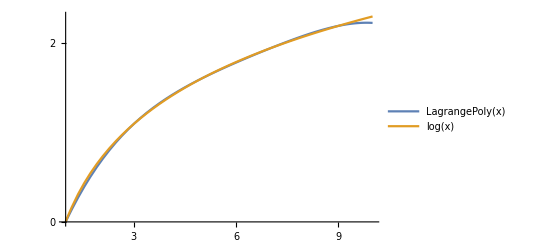

```mathematica
abscissas={1,3,5,7,9};
functionvalues={N[Log[1]],N[Log[3]],N[Log[5]],N[Log[7]],N[Log[9]]};
LagrangePoly[x_]=Simplify[LagrangePoly[abscissas,functionvalues]];
Print["Lagrange Polynomial = ",LagrangePoly[x]];
Plot[{LagrangePoly[x],Log[x]},{x,1,10},Ticks->{Range[0,10]},PlotLegends->"Expressions"]
```